## DivideCell-example.nb

Example Cellzilla2D notebook

GPL License applies.
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Warning: Cellzilla2D: xSSA.m not found in path. Some stochastic conversion functions may not work as expected. It should be loaded manually before any xSSA (stochastic) simulations can be run.

Cellzilla2D (3.0.51 (05 June 2017)) loaded Wed 7 Jun 2017 11:05:10
using xCellerator 0.95 and XSSA ** Not Found **
GPL License Terms Apply

```mathematica
w=TemplateRandom[5, {{0,0}, {10,0}, {11, 10}, {-1, 10}}];
```

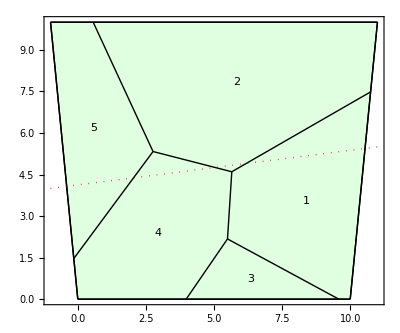

```mathematica
ShowTissue[w, "CellNumbers"-> True, Frame-> True, 
Epilog->{Thick, Red, Dotted, Line[{{-1,4}, {15, 6}}]}]
```

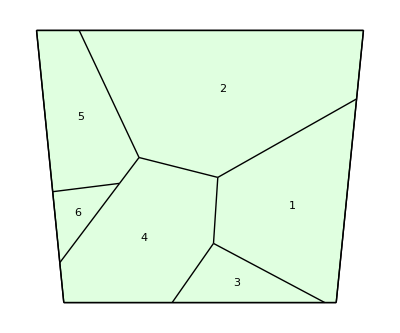

```mathematica
w1=DivideCell[w, 5, {{-1,4}, {15,6}}]; 
ShowTissue[w1, "CellNumbers"-> True]
```